# Parâmetros unitários de um circuito de 138 kV

## Antonio Carlos Siqueira de Lima EEE457 (PLE 2020)

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/Transmissão-2020/arquivos_MMA_EE457

```mathematica
markers1={{Thick,Darker@Red,Line[{{1,0},{3,0}}]}};
markers2={{Thick,Darker@Green, Dotted,Line[{{1,0},{3,0}}]}};
markers3={{Thick,Darker@Blue, Dashed,Line[{{1,0},{3,0}}]}};
markers4 ={{Thick,Darker@Cyan,Line[{{1,0},{3,0}}]}};
markers5={{Thick,Darker@Magenta, Dotted,Line[{{1,0},{3,0}}]}};
markers6= {{Thick,Darker@Yellow, Dashed,Line[{{1,0},{3,0}}]}};
markers7 ={{Thick,Darker@Black,Line[{{1,0},{3,0}}]}};
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,PlotStyle-> {markers1,markers2,markers3,markers4,markers5,markers6,markers7},
Axes-> False,Frame-> True,PlotRange->All];
```

## Funções para os cálculos

```mathematica
(* impedancia interna de condutores tubulares *)
ZintTubo[Omega_,Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
       Module[{r},  With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]],ri=rint+10^-6}, 
        With[{Den = BesselK[1,Etac*ri]*BesselI[1,Etac*rf]-BesselK[1,Etac*rf]*BesselI[1,Etac*ri], 
             Num =  BesselK[1,Etac*ri]*BesselI[0,Etac*rf]+BesselK[0,Etac*rf]*BesselI[1,Etac*ri]}, 
        ((Rhoc*Etac)*Num)/((2*Pi*rf)*Den)]]]
```

```mathematica
(* impedancia interna de condutores cilindricos sólidos *) 
(*Mur=80 para cables de acero*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:80, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
(* Matriz de Coeficientes de Potencial *)
MPot[x_?VectorQ,y_?VectorQ,nc_,npr_,rf_,rpr_]:=Table[If[i!=j,
1./2 Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],
If[i<=nc-npr,
Log[(2 y[[i]])/rf],
Log[(2 y[[i]])/rpr]]],{i,nc},{j,nc}]
```

```mathematica
(* Matriz de Impedância de Retorno Pelo Solo *)
```

```mathematica
S1[x_?VectorQ,y_?VectorQ,nc_,npr_,rf_,rpr_,γs_,γar_]:=
With[{η= Sqrt[γs^2-γar^2]},
Table[If[i!=j,
Log[2./(η Sqrt[(x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2])+1],
If[i<=nc-npr,
Log[2/(η Sqrt[4*y[[i]]^2+rf^2])+1],
Log[2/(η Sqrt[4*y[[i]]^2+rpr^2])+1]]],{i,nc},{j,nc}]]
```

## Configuração da Rede

```mathematica
Rdcf=0.17*10^-3 ;
Rdcpr=4.19*10^-3;
rf=18.29/2 10^-3;
rpr=4.57*10^-3;
xc={-3.8,3.8,-3.8,0};
yc={21.2, 23.1, 21.2+3.8, 21.2+3.8+5.6 };
fl={9.25, 9.25, 9.25 ,4.7};
(* usando a altura media *)
yc=yc-2/3 fl;
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-10,10},{5,40.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

```mathematica
ncond=Length[xc];
nfases=3;
npr=1;
nc = ncond;
```

### Circuito 138 kV (Penguin)

```mathematica
rf=7.1501*10^-3;
rint=2.3876*10^-3;
Rdc=35.356020838304296*10^-5 ;
ρc=Rdc* π* (rf^2-rint^2);
```

### Circuito 3/8 EHS (C.G.)

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
ρpr=Rdcpr*π *rpr^2;
```

### Outros dados

```mathematica
ϵ=8.854 10^-12;
μ= 4.0 π 10^-7;
σs=1 10.0^-3;
ϵr=10.0;
compr=50000.0;
```

Freqüências de interesse

```mathematica
freq= 60.0;
```

Cálculo dos parâmetros

```mathematica
ω=2 π freq; 
γs=Sqrt[ⅉ ω μ (σs+ⅉ ω ϵr ϵ)];
γar=ⅉ ω Sqrt[μ ϵ];
m=MPot[xc,yc,ncond,npr,rf,rpr];
zin=DiagonalMatrix[Table[If[i≤ ncond-npr,ZintTubo[ω,ρc,rf,rint],Zin[ω,ρpr,rpr]],{i,ncond}]];
(*--------------------matrizes  ---------------------------------------*)
s1=S1[xc,yc,ncond,npr,rf,rpr,γs,γar];

z1 =zin+ⅉ ω μ/(2 π)(m+s1);

y1=3.0*10^-11 DiagonalMatrix[Table[1,{ncond}]]+ⅉ ω 2 π ϵ Inverse[m];
```

## Resultados

### Matriz de impedânica (longitudinal) por unidade de comprimento em Ω/km

```mathematica
MatrixForm@(z1 1000)
```

(0.412464+0.98974 ⅈ | 0.0586207+0.446658 ⅈ | 0.0586025+0.501224 ⅈ | 0.0584439+0.408643 ⅈ
0.0586207+0.446658 ⅈ | 0.412396+0.98981 ⅈ | 0.0585538+0.446726 ⅈ | 0.0584099+0.419936 ⅈ
0.0586025+0.501224 ⅈ | 0.0585538+0.446726 ⅈ | 0.412327+0.98988 ⅈ | 0.0583759+0.432905 ⅈ
0.0584439+0.408643 ⅈ | 0.0584099+0.419936 ⅈ | 0.0583759+0.432905 ⅈ | 4.42311+2.48512 ⅈ)

### Matriz de admitânica (transversal) por unidade de comprimento em S/km

```mathematica
MatrixForm@(y1 1000)
```

(3.×10^-8+2.75688×10^-6 ⅈ | 0.-3.23951×10^-7 ⅈ | 0.-6.08674×10^-7 ⅈ | 0.-1.97839×10^-7 ⅈ
0.-3.23951×10^-7 ⅈ | 3.×10^-8+2.64193×10^-6 ⅈ | 0.-3.38325×10^-7 ⅈ | 0.-2.90019×10^-7 ⅈ
0.-6.08674×10^-7 ⅈ | 0.-3.38325×10^-7 ⅈ | 3.×10^-8+2.72606×10^-6 ⅈ | 0.-3.35899×10^-7 ⅈ
0.-1.97839×10^-7 ⅈ | 0.-2.90019×10^-7 ⅈ | 0.-3.35899×10^-7 ⅈ | 3.×10^-8+2.35713×10^-6 ⅈ)

### Matrizes de sequência

```mathematica
a= Exp[I 120 Degree];
A ={{1,1,1},{1,a^2, a},{1,a, a^2}};
```

```mathematica
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Zabc= z1[[1;;3,1;;3]];
Yabc=y1[[1;;3,1;;3]];
```

```mathematica
z012=Inverse[A].Zabc.A;
```

```mathematica
y012=Inverse[A].Yabc.A;
```

## Valores de Sequência

```mathematica
zpos= z012[[2,2]];
ypos = y012[[2,2]];
```

## Impedância caracterísitca

```mathematica
Vn  =138.;
Zc = Sqrt[zpos/ypos];
```

```mathematica
Arg[Zc]180/π
```

-16.7153

```mathematica
Sn = Vn^2/Zc
```

40.5704+12.1835 ⅈ

```mathematica
Pn=Re[Sn]
```

40.5704

Notem que a parte imaginária da potência aparente  “natural” da linha indica que a mesma gera reativos, e a potência “natural”  do circuito é de 40 MW

## Comparações entre os Modelos de Quadripolo

```mathematica
γ = Sqrt[ zpos ypos];
a = Cosh[ γ compr];
b = Zc Sinh[γ compr];
c = 1/Zc Sinh[γ compr];
```

```mathematica
q ={{a, b},{c, a}};
MatrixForm[q]
```

(0.997959+0.00140384 ⅈ | 17.6658+26.2375 ⅈ
1.42568×10^-6+0.000156491 ⅈ | 0.997959+0.00140384 ⅈ)

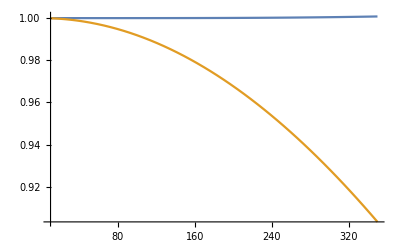

```mathematica
Plot[ {Abs[Cosh[γ x 10^3]] / Abs[   (1 + (zpos x ypos  x  10^6)/2)],Abs[Cosh[γ x 10^3]] },{x, 10, 350}, PlotRange->All]
```

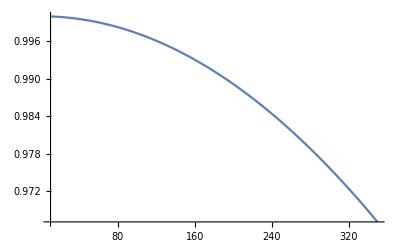

```mathematica
Plot[ {Abs[Zc Sinh [γ x 10^3]] / Abs[ zpos   x  10^3]},{x, 10, 350}, PlotRange->All]
```

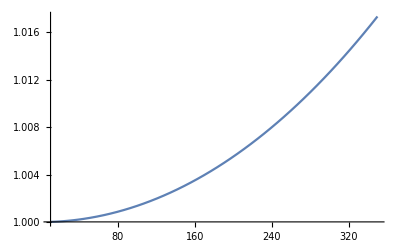

```mathematica
Plot[ {Abs[1/ Zc Sinh [γ x 10^3]] / Abs[  ypos x 10^3  (1 +zpos x 10^3  ypos x 10^3/4)]},{x, 10, 350}, PlotRange->All]
```